DATA STRUCTURE SORTING ALGORITHMS AND  TIME COMPLEXITY

Name: Harshad Kumar Elangovan																
																 	   Course:Data and Computational Science
																			Student ID: 19200349
														Topic:Data structure Sorting Algorithms and its Time Complexity

Objective:
The objective of this project is to compare and execute the sorting algorithms on a list of random values and conclude the fastest among the defined algorithms.

Data Structure is a concept of Data organization, management and storage format that helps in efficient functioning of the block of codes for a particular task.One part of Data organization in Data Structure is the sorting Algorithms.
There are several Sorting Algorithms that sort data based on unique methods. Few of the sorting algorithms are,

Selection Sort

Bubble Sort

Insertion Sort

Quick Sort

Merge Sort

Heap Sort,etc.

In this project, we will have a look at four Sorting algorithms

Selection Sort

Insertion Sort

Bubble Sort

Quick Sort.

```mathematica
(*ClearAll["Global`*"]*)
```

Selection Sort Algorithm:
Selection Sort Algorithm sorts the list of values by repeatedly finding the minimum element from unsorted list and swaps it to the beginning of the list.Once the sorting is done, the elements are placed in the ascending order.

```mathematica
selectionSort[values1_]:= Module[{listval=values1,i,j,temp,n=Length[values1]},
For[i=0,i < n  ,i++;
temp=i;
(*Print[listval[[i]]]*) (*These print statements can be used as a debugging step while running the function.*)
For[j=i,j <n ,j++;
	If[listval[[j]]<listval[[temp]],
	(*Print[listval[[j]]];Print[listval[[j]]];*)
		temp=j;
];
];
(*Print[listval[[{i,temp}]]];*)
listval[[{i,temp}]]=listval[[{temp,i}]];
(*listval*)
];
listval
]
```

Insertion Sort Algorithm:
This type of sorting method works on all the values of the list. It compares the element with other elements in list and inserts it to the existing list.

```mathematica
insertionSort[values1_]:= Module[{listval=values1,i,j,temp,n = Length[values1]},
For[i=1,i<n,i++;
temp=listval[[i]];
j=i;
While[j>0 && (temp<listval[[j-1]]),
listval[[j]]=listval[[j-1]];
j--];
listval[[j]]=temp;
];
listval
]
```

Bubble Sort Algorithm:
This is the simplest sorting Algorithm which is executed by comparing and swapping the elements in the list based on the order. If number is larger than the number next to it, then it is swapped and the smaller numbers are placed in ascending order.

```mathematica
bubbleSort[values1_]:=Module[{listval=values1,i,j,temp,n=Length[values1]},
For[i=0,i <  n-1,i++;
	For[j=0,j<(n-i),j++;
If[listval[[j]] > listval[[j+1]],
temp = listval[[j]];
listval[[j]] = listval[[j+1]];
listval[[j+1]]=temp;
];
];
];
listval
]
```

Quick Sort Algorithm:
The Quick Sort is a type of Divide and COnquer Algorithm which picks the elements as pivot and splits the list and sorts the sublists seperately. This partition of values helps in re-arranging the values in the both the sublists and then combines it to form a complete sorted list.

```mathematica
quickSort[list_]:= Module[{listval=list},
listval=subSort[listval,1,Length[listval]];
listval
]
subSort[values_,start_,end_]:= Module[{llist=values,pivot=values[[Floor[(start+end)/2]]],i=start,j=end},
While[True,
While[llist[[i]]<pivot,i++];
While[llist[[j]]>pivot,j--];
If[i≥ j,Break[]];
llist=swap[llist,i,j];
i=start;
j=end;
pivot=llist[[Floor[(start+end)/2]]]];
Flatten[ If[start≠end,
		{If[start==Floor[(start+end)/2],
			llist[[start]],
			subSort[llist,start,Floor[(start+end)/2]]],
			  If[end==Floor[(start+end)/2],llist[[end]],subSort[llist,Floor[(start+end)/2]+1,end]]},
	{llist[[start]]}]]
]
swap[list_,i_,j_]:= Module[{l=list},{l[[i]],l[[j]]}={l[[j]],l[[i]]};
l
]
```

Random Values Generation:
In this project, I’ve taken four different range of random values and used these sorting algorithms to check the duration in which the functions sort the list of random values. In other words, this is done to check the time complexity of the algorithms.

```mathematica
randomvalues10000=RandomSample[Range[100000],10000];
```

```mathematica
randomvalues50000=RandomSample[Range[1000000],50000];
```

```mathematica
randomvalues1000 = RandomSample[Range[10000],1000];
```

```mathematica
randomvalues10=RandomSample[Range[100],10]
```

{92,83,62,94,11,72,43,36,75,22}

Sorting 10 Random Values:

```mathematica
selectionsort10=selectionSort[randomvalues10]//Timing
insertionsort10=Timing[insertionSort[randomvalues10]];
bubblesort10= Timing[bubbleSort[randomvalues10]];
quicksort10=Timing[quickSort[randomvalues10]];
```

{0.,{11,22,36,43,62,72,75,83,92,94}}

Sorting 1000 Random Values:

```mathematica
selectionsort1000=Timing[selectionSort[randomvalues1000]]
insertionsort1000=Timing[insertionSort[randomvalues1000]];
bubblesort1000= Timing[bubbleSort[randomvalues1000]];
quicksort1000=Timing[quickSort[randomvalues1000]];
```

{0.59375,{3,7,48,69,78,79,84,87,109,122,138,151,200,219,220,268,282,304,310,313,315,317,318,319,327,329,333,350,352,355,367,368,381,410,417,426,441,485,488,492,524,529,531,532,541,542,545,552,579,582,583,593,622,630,634,647,659,671,679,682,686,688,692,699,706,731,740,741,762,773,782,783,789,798,805,819,852,865,866,879,882,892,902,912,918,921,924,928,958,984,992,1003,1009,1012,1024,1027,1034,1062,1063,1064,1088,1093,1100,1105,1111,1121,1122,1124,1132,1149,1156,1170,1176,1179,1201,1206,1226,1235,1246,1247,1251,1253,1254,1257,1267,1275,1283,1311,1330,1332,1340,1341,1374,1383,1395,1398,1415,1418,1420,1425,1430,1431,1439,1441,1445,1448,1461,1478,1489,1499,1553,1574,1575,1583,1584,1590,1605,1616,1619,1621,1623,1632,1648,1656,1660,1679,1690,1732,1740,1752,1758,1762,1766,1768,1790,1803,1808,1817,1835,1860,1864,1866,1867,1899,1901,1903,1904,1914,1932,1936,1937,1958,1972,1979,1993,1998,2000,2005,2015,2021,2028,2029,2042,2058,2064,2073,2075,2086,2087,2094,2099,2103,2111,2123,2133,2164,2178,2196,2209,2211,2219,2226,2232,2233,2237,2251,2256,2268,2271,2279,2281,2289,2292,2299,2301,2305,2306,2330,2339,2346,2349,2382,2394,2407,2408,2420,2421,2438,2442,2443,2449,2455,2466,2469,2472,2473,2476,2540,2551,2563,2566,2569,2578,2589,2620,2634,2647,2648,2659,2680,2692,2695,2696,2698,2699,2718,2726,2728,2760,2764,2797,2804,2807,2817,2830,2835,2837,2847,2876,2888,2894,2903,2921,2928,2939,2946,2964,2977,2984,2990,2997,3019,3020,3039,3065,3095,3098,3108,3111,3117,3119,3127,3129,3136,3137,3139,3162,3182,3206,3211,3213,3216,3223,3234,3241,3244,3256,3257,3259,3262,3311,3323,3330,3332,3345,3376,3378,3383,3385,3387,3389,3392,3424,3450,3454,3456,3466,3470,3477,3510,3527,3536,3543,3549,3550,3554,3556,3573,3599,3601,3610,3613,3625,3633,3647,3649,3677,3678,3687,3692,3710,3726,3753,3789,3793,3797,3801,3807,3822,3824,3830,3831,3833,3838,3847,3856,3857,3862,3887,3891,3901,3914,3919,3942,3945,3952,3966,3980,3997,4001,4010,4017,4041,4044,4048,4061,4086,4091,4095,4113,4115,4116,4136,4138,4146,4155,4167,4190,4198,4218,4222,4233,4238,4240,4299,4302,4339,4341,4350,4351,4355,4357,4365,4367,4372,4382,4397,4403,4407,4424,4448,4493,4497,4498,4499,4501,4505,4506,4511,4525,4527,4530,4534,4553,4556,4557,4567,4571,4576,4577,4578,4583,4585,4589,4602,4610,4611,4643,4663,4668,4671,4680,4701,4704,4726,4730,4735,4740,4745,4748,4759,4761,4772,4778,4781,4822,4824,4834,4863,4877,4899,4901,4914,4937,4941,4942,4959,4973,4974,4980,4985,4990,4997,5026,5034,5040,5048,5053,5061,5080,5141,5142,5154,5155,5158,5161,5173,5195,5223,5230,5233,5234,5242,5247,5267,5272,5282,5305,5306,5310,5321,5343,5345,5346,5350,5358,5372,5377,5388,5396,5399,5421,5424,5430,5450,5460,5472,5477,5487,5489,5506,5523,5538,5542,5558,5564,5589,5603,5605,5615,5616,5623,5640,5643,5651,5653,5656,5657,5670,5672,5690,5707,5710,5714,5720,5728,5743,5755,5774,5790,5795,5796,5819,5822,5858,5872,5880,5886,5916,5924,5925,5929,5935,5951,5977,5997,5998,6005,6008,6018,6021,6032,6037,6040,6041,6042,6043,6049,6061,6071,6074,6079,6089,6116,6132,6140,6147,6148,6152,6156,6161,6163,6167,6183,6192,6204,6215,6218,6222,6236,6243,6250,6274,6278,6279,6285,6298,6299,6302,6304,6310,6319,6339,6347,6350,6355,6383,6392,6405,6406,6427,6439,6465,6473,6477,6490,6494,6503,6514,6521,6523,6527,6529,6550,6559,6570,6572,6573,6579,6586,6588,6595,6599,6608,6610,6632,6636,6637,6643,6646,6650,6654,6657,6663,6667,6668,6674,6682,6688,6690,6695,6696,6697,6705,6711,6713,6721,6726,6749,6758,6773,6777,6787,6804,6816,6824,6842,6848,6862,6873,6883,6898,6910,6914,6916,6918,6921,6928,6933,6941,6946,6992,6993,6997,7031,7039,7054,7057,7078,7091,7094,7095,7098,7106,7109,7141,7144,7164,7176,7188,7200,7205,7219,7241,7253,7262,7285,7301,7310,7312,7316,7322,7329,7346,7353,7378,7387,7388,7391,7400,7410,7430,7435,7444,7445,7456,7476,7479,7481,7486,7495,7501,7516,7526,7535,7555,7556,7563,7566,7569,7586,7612,7625,7640,7664,7677,7687,7688,7694,7714,7723,7763,7770,7795,7810,7829,7846,7848,7863,7891,7902,7919,7927,7932,7936,7969,7984,8005,8008,8037,8038,8044,8048,8055,8057,8058,8076,8082,8096,8127,8131,8173,8175,8179,8189,8200,8204,8205,8211,8215,8216,8219,8245,8259,8261,8263,8267,8303,8306,8318,8323,8336,8350,8366,8371,8373,8399,8400,8426,8434,8438,8444,8446,8447,8448,8453,8455,8462,8463,8466,8481,8493,8494,8495,8506,8519,8526,8548,8558,8568,8580,8584,8592,8593,8597,8601,8608,8612,8620,8624,8631,8655,8669,8694,8703,8706,8720,8728,8734,8737,8765,8770,8771,8782,8790,8796,8797,8800,8804,8816,8829,8831,8841,8869,8888,8896,8904,8908,8933,8998,9006,9016,9018,9042,9044,9057,9059,9070,9084,9098,9103,9116,9120,9121,9140,9163,9174,9178,9180,9185,9200,9204,9210,9214,9220,9257,9282,9288,9297,9309,9314,9327,9353,9371,9373,9381,9402,9424,9431,9438,9485,9486,9492,9506,9511,9512,9515,9521,9541,9542,9574,9576,9577,9591,9597,9602,9604,9616,9636,9648,9652,9657,9662,9682,9697,9698,9711,9723,9728,9730,9732,9747,9753,9775,9792,9814,9823,9825,9833,9834,9850,9893,9910,9939,9959,9960,9973,9982,9983,9986}}

Sorting 10,000 Random Values:

```mathematica
ClearSystemCache[]
selectionsort10000=Timing[selectionSort[randomvalues10000]];
insertionsort10000=Timing[insertionSort[randomvalues10000]];
bubblesort10000= Timing[bubbleSort[randomvalues10000]];
quicksort10000=Timing[quickSort[randomvalues10000]];
```

Sorting 50,000 Random Values:

```mathematica
ClearSystemCache[]
```

```mathematica
selectionsort50000=Timing[selectionSort[randomvalues50000]];(* Sorting 50,000 values takes more time compared with other data range.*)
```

```mathematica
insertionsort50000=Timing[insertionSort[randomvalues50000]];
```

```mathematica
bubblesort50000= Timing[bubbleSort[randomvalues50000]];
```

```mathematica
quicksort50000=Timing[quickSort[randomvalues50000]];
```

```mathematica
selectionsort50000
```

{1909.16,{7,61,74,108,120,174,190,196,225,244,265,318,329,359,368,374,402,412,416,440,463,497,525,541,550,592,599,613,640,663,669,676,719,722,724,838,844,858,922,929,973,1000,1022,1028,1037,1046,1058,1064,1102,1149,1181,1221,1284,1285,1291,1292,1307,1329,1346,1350,1356,1401,1414,49874,998778,998802,998804,998855,998856,998880,998892,998897,998913,998928,998932,998953,998986,999130,999140,999155,999156,999184,999189,999207,999209,999227,999229,999245,999258,999290,999293,999298,999316,999349,999362,999368,999398,999418,999440,999470,999472,999528,999531,999537,999540,999560,999569,999570,999576,999591,999604,999615,999640,999643,999646,999648,999666,999667,999704,999714,999722,999740,999817,999849,999907,999923,999938}}
 |  |  |  |

```mathematica
insertionsort50000
```

{1621.55,{7,61,74,108,120,174,190,196,225,244,265,318,329,359,368,374,402,412,416,440,463,497,525,541,550,592,599,613,640,663,669,676,719,722,724,838,844,858,922,929,973,1000,1022,1028,1037,1046,1058,1064,1102,1149,1181,1221,1284,1285,1291,1292,1307,1329,1346,1350,1356,1401,1414,49874,998778,998802,998804,998855,998856,998880,998892,998897,998913,998928,998932,998953,998986,999130,999140,999155,999156,999184,999189,999207,999209,999227,999229,999245,999258,999290,999293,999298,999316,999349,999362,999368,999398,999418,999440,999470,999472,999528,999531,999537,999540,999560,999569,999570,999576,999591,999604,999615,999640,999643,999646,999648,999666,999667,999704,999714,999722,999740,999817,999849,999907,999923,999938}}
 |  |  |  |

```mathematica
bubblesort50000
```

{4670.83,{6,26,51,58,60,89,93,95,156,174,184,207,236,278,294,302,360,385,434,474,517,529,580,636,645,655,677,680,711,719,720,769,770,833,838,867,915,916,921,924,947,957,971,982,989,1003,1026,1055,1063,1073,1090,1150,1163,1177,1192,1225,1247,1267,1292,1342,1345,1379,1382,1392,49872,998721,998731,998735,998763,998826,998831,998845,998852,998865,998885,998920,998927,998945,998952,998985,998986,999024,999030,999036,999095,999097,999106,999114,999115,999129,999141,999161,999216,999235,999262,999281,999353,999356,999370,999391,999427,999496,999506,999514,999517,999526,999563,999600,999606,999623,999640,999655,999687,999692,999716,999719,999726,999752,999810,999815,999844,999861,999873,999887,999895,999932,999941,999951,999959}}
 |  |  |  |

```mathematica
quicksort50000
```

{626.891,{7,61,74,108,120,174,190,196,225,244,265,318,329,359,368,374,402,412,416,440,463,497,525,541,550,592,599,613,640,663,669,676,719,722,724,838,844,858,922,929,973,1000,1022,1028,1037,1046,1058,1064,1102,1149,1181,1221,1284,1285,1291,1292,1307,1329,1346,1350,1356,1401,1414,49874,998778,998802,998804,998855,998856,998880,998892,998897,998913,998928,998932,998953,998986,999130,999140,999155,999156,999184,999189,999207,999209,999227,999229,999245,999258,999290,999293,999298,999316,999349,999362,999368,999398,999418,999440,999470,999472,999528,999531,999537,999540,999560,999569,999570,999576,999591,999604,999615,999640,999643,999646,999648,999666,999667,999704,999714,999722,999740,999817,999849,999907,999923,999938}}
 |  |  |  |

Table of time taken by each Algorithm for all the list range

```mathematica
data={{"10 Random Values",selectionsort10[[1]],insertionsort10[[1]],bubblesort10[[1]],quicksort10[[1]]},{"1000 Random Values",selectionsort1000[[1]],insertionsort1000[[1]],bubblesort1000[[1]],quicksort1000[[1]]},{"10,000 Random Values",selectionsort10000[[1]],insertionsort10000[[1]],bubblesort10000[[1]],quicksort10000[[1]]},{"50,000 Random Values",selectionsort50000[[1]],insertionsort50000[[1]],bubblesort50000[[1]],quicksort50000[[1]]}};
(*{"50,000 Random Values",1664.484375,1288.53125,3963.515625,551.234375}}; The values vary based on the use of internal system caches,which can be cleared with clear system cache*)
```

```mathematica
data
```

{{10 Random Values,0.,0.,0.,0.},{1000 Random Values,0.703125,0.5625,1.5,0.28125},{10,000 Random Values,70.5156,56.3438,155.547,23.0313},{50,000 Random Values,1909.16,1621.55,4117.,626.891}}

The time complexity of the lower data range list is approximately equal to zero since all the algorithms sort the list with minimal time. But as the range increases, the time complexity increases. This become evident from the timing difference between the four Algorithms.

```mathematica
Text@Grid[Prepend[data,{"Count of Random Values","Selection Sort","Insertion Sort","Bubble Sort","Quick Sort"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->{Center},ItemSize->{{20,10,10,10}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

Count of Random Values | Selection Sort | Insertion Sort | Bubble Sort | Quick Sort
10 Random Values | 0. | 0. | 0. | 0.
1000 Random Values | 0.59375 | 0.515625 | 1.34375 | 0.25
10,000 Random Values | 61.1875 | 51.9844 | 142.516 | 21.1719
50,000 Random Values | 1761.17 | 1419.88 | 4670.83 | 552.563

Manipulate for calculating the time range among the four Algorithms based on interactive range up to 5000 and its random samples.

```mathematica
F1[x_,y_]:={Timing[selectionSort[RandomSample[Range[x],y]]][[1]],Timing[insertionSort[RandomSample[Range[x],y]]][[1]],Timing[bubbleSort[RandomSample[Range[x],y]]][[1]],Timing[quickSort[RandomSample[Range[x],y]]][[1]]}
Manipulate[F1[i,j],{{i,1,"Range"},1,5000,1},{{j,1,"Random Samples"},1,i-1,1}]
```

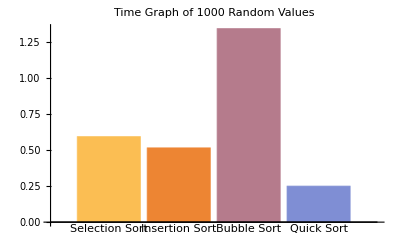

```mathematica
BarChart[{{selectionsort1000[[1]],insertionsort1000[[1]],bubblesort1000[[1]],quicksort1000[[1]]}},ChartLabels->{"Selection Sort","Insertion Sort","Bubble Sort","Quick Sort"},Axes->True,PlotLabel->"Time Graph of 1000 Random Values"]
```

```mathematica
Manipulate[BarChart[{data[[i,2;;5]]},ChartLabels->{"Selection Sort","Insertion Sort","Bubble Sort","Quick Sort"},Axes->True,Frame->True,FrameLabel->{"Sorting Algorithms","Time"},ChartBaseStyle->EdgeForm[Dashed],PlotLabel->data[[i]][[1]]],{{i,1,"Sorting Algorithm"},1,4,1}]
(*Export["C:\\Users\\harshie\\Documents\\UCD\\Mathematica\\ProjectV1\\19200349\\SortingBarPlot",%];This will export the below Bar Plot to a GIF format to the suggested location. *)
```

```mathematica
F2[x_,y_]:={Timing[selectionSort[RandomSample[Range[x],y]]][[1]],Timing[insertionSort[RandomSample[Range[x],y]]][[1]],Timing[bubbleSort[RandomSample[Range[x],y]]][[1]],Timing[quickSort[RandomSample[Range[x],y]]][[1]]}
Manipulate[DiscretePlot[F2[i,j][[k]],{k,1,4},ExtentSize->All,PlotMarkers->Automatic,PlotLabel->"TIME COMPLEXITY CHART",Axes->True,PlotRange->{{0,5},{0,3}}],{{i,1,"Range"},1,1500,1},{{j,1,"Random Samples"},1,i-1,1}] (*The plotting may take some time as the range and random samples increase*)
```

From the above discrete plot, we can compare the result with the tabular representation of the time complexity of all the sorting algorithms in the Data Structure.

```mathematica
Import["C:\\Users\\harshie\\Documents\\UCD\\Mathematica\\ProjectV1\\19200349\\TimeComplexityofAlgorithms.JPG",ImageSize->Large]
```

-Graphics-

CONCLUSION:

As a whole, Quick Sort Algorithm is the fastest among all the other three algorithms. The time complexity of this algorithm is O(NlogN) which is the best when compared with the rest. The time complexity of Insertion sort is O(N^2) which comes after quick sort in sorting the data.The sorting algorithm after Insertion sort will be Selection sort with time complexity O(N^2) and the last will be Bubble Sort. So, the bubble sort is the slowest as it compares each element with the entire values in the list.